## Using equidistant positions on the mesh

```mathematica
img=Import["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi pos\\15\\Mask2.tif"];
```

```mathematica
img=GaussianFilter[Erosion[-Graphics-,1],20]//Binarize;
```

```mathematica
R=ImageMesh[img,Method->"Exact"];
polygon=Append[#,#[[1]]]&@MeshCoordinates[R][[ MeshCells[R,2][[1,1]] ]];
t=Prepend[Accumulate[Norm/@Differences[polygon]],0.];
γ=Interpolation[Transpose[{t,polygon}],InterpolationOrder->1,PeriodicInterpolation->True];
s=Subdivide[γ[[1,1,1]],γ[[1,1,2]],300];
newpts=γ[s];
```

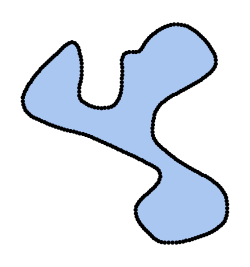

```mathematica
Show[R,Graphics@Point@newpts,ImageSize-> 250]
```

```mathematica
shiftPairs[perimeter_,shift_]:=Module[{newls},
newls=perimeter[[-shift;;]]~Join~perimeter~Join~perimeter[[;;shift]];Table[{newls[[i-shift]],newls[[i]],newls[[i+shift]]},{i,1+shift,Length[newls]-shift}]
];
```

```mathematica
perimeter=newpts;
pairs=shiftPairs[perimeter,14];
```

```mathematica
penalty[c_,radius_,pts_]:=(Map[radius-Norm[#-c]&,pts])^2//Total;

circleFits[pts_]:=Block[{res,x,y,rr,circ},
res=Minimize[penalty[{x,y},rr,pts],{x,y,rr}];
Circle[{x,y},rr]/.(res//Last)
];
```

```mathematica
circles=circleFits/@pairs;
```

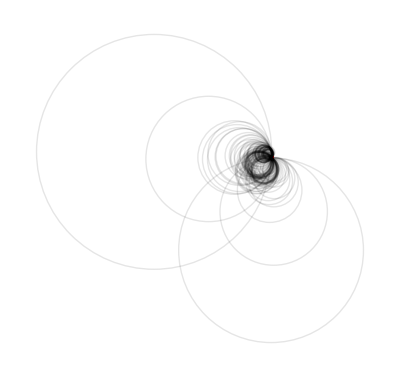

```mathematica
Graphics[{{Red,Point@perimeter},{XYZColor[0,0,0,0.1],circles}}]
```

```mathematica
κ= 1/Cases[circles,x_Circle:> Last@x];
midpoints=Midpoint/@pairs[[All,{1,-1}]];
regionmembership=RegionMember[R,midpoints]/.{True-> 1,False-> -1};
κ*=regionmembership;
```

```mathematica
Apply[Equal,Length/@{perimeter,κ}]
```

True

```mathematica
col=ColorData["Rainbow"]/@Rescale[κ,MinMax[κ],{0,1}];
g=Graphics[{PointSize[0.010],MapThread[Point[#1,VertexColors->#2]&,{perimeter,col}]}];
```

```mathematica
Show[img,g,ImageSize-> Large]
```

-Graphics-

## script

```mathematica
<<"C:\\Users\\aliha\\Desktop\\curvatureMeasure.m";
```

```mathematica
img=GaussianFilter[Erosion[-Graphics-,1],20]//Binarize;
```

-Graphics-

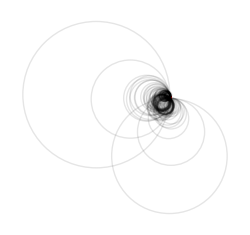

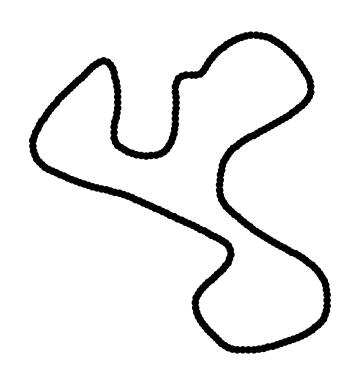

{0.0000245675,0.0000316065,0.0000354131,0.0000367233,0.0000365952,0.0000365964,0.0000340364,0.0000272773,0.0000256213,0.0000290639,0.0000313901,0.0000322,0.0000337454,0.0000343819,0.0000326803,0.0000334043,0.0000352117,0.0000372099,0.000038451,0.0000413038,0.0000463931,0.0000553656,-0.000353157,-0.000528785,-0.000814169,-0.00123163,-0.00142117,-0.00154108,-0.00166794,-0.00143059,-0.00152935,-0.00139922,-0.00145009,-0.00134914,-0.0012027,-0.00130734,-0.000945137,-0.000952653,-0.000737182,-0.00078331,-0.000796832,-0.00152583,-0.00231546,-0.00370102,-0.00503766,-0.00665365,-0.00819324,-0.0103893,-0.0123602,-0.0140419,-0.0157821,-0.0172332,-0.0181003,-0.0185456,-0.0187957,-0.0187111,-0.0185979,-0.0179893,-0.0169591,-0.0155554,-0.0138343,-0.0110211,-0.00774408,-0.0040768,0.000142819,0.0000366949,0.0000287138,0.0000245055,0.0000216124,0.0000196667,3.88842×10^-6,0.0000124158,0.0000142795,0.0000265405,0.0000335695,0.000030907,0.0000378128,0.0000364478,0.0000224088,0.0000216696,0.0000320602,0.00003356,0.0000336898,0.0000337696,0.0000325045,0.0000310471,0.0000296796,0.0000263887,0.0000212754,0.0000195497,0.0000141632,4.94746×10^-6,8.51213×10^-6,0.000018662,0.0000223402,0.0000311202,0.0000381908,0.0000354424,0.00859943,0.00905485,0.00969667,0.0102926,0.0111057,0.0119067,0.012631,0.0132961,0.014053,0.0146898,0.0152703,0.0155786,0.0158415,0.0159884,0.0159407,0.0159734,0.0156082,0.0152411,0.0147636,0.0140923,0.0133203,0.0125703,0.0115036,0.0105594,0.00934552,0.00853841,0.00758805,0.00644644,0.00547305,0.00389094,0.00292407,0.00181721,0.000910283,0.000227041,-0.0000490559,-0.0000401431,-0.0000352463,-0.0000373264,-0.0000329328,-0.0000306813,-0.0000278113,-0.0000222045,-0.0000230174,-0.0000281899,-0.0000301155,-0.0000313211,-0.0000329159,-0.0000338317,-0.0000334231,-0.0000329255,-0.0000324021,-0.0000306041,-0.0000276316,-0.0000222041,-0.0000132441,-0.0000162027,-0.0000223026,-0.0000287869,-0.0000366624,-0.0000374211,-0.0000466768,-0.0000525399,-0.000053364,-0.0000463636,-0.0000643087,-0.0000675991,-0.0000665727,-0.0000657667,-0.0000786544,-0.0000915775,-0.0000914678,-0.000107676,-0.000150228,0.000462091,0.00208367,0.00373214,0.00539439,0.00709625,0.008643,0.0103065,0.0115142,0.0129088,0.013931,0.0148954,0.0156735,0.016253,0.0165606,0.0168235,0.0169375,0.0168859,0.0166414,0.01635,0.015964,0.015413,0.0150772,0.0145276,0.0142321,0.0136183,0.0132548,0.0129534,0.0127115,0.0126696,0.0126093,0.0127846,0.0130749,0.0134119,0.0135403,0.0137198,0.0137448,0.0136314,0.0131443,0.0122124,0.0110553,0.00943352,0.00817205,0.00698242,0.00661726,0.0000779276,0.0000802973,0.0000963898,0.0000924509,0.0000732533,0.0000919838,0.0000899937,0.000067858,0.000060526,0.0000648956,0.0000543047,0.0000546344,0.0000525674,0.0000510061,0.0000517382,0.0000516188,0.0000639681,0.0000859381,0.000132234,-0.00120769,-0.0038625,-0.00673107,-0.00939976,-0.0116877,-0.0134933,-0.0147319,-0.0158871,-0.0169884,-0.0182629,-0.0193971,-0.020274,-0.0214082,-0.02196,-0.0223353,-0.0218608,-0.0210252,-0.0000248397,-0.0000365252,-0.0000400852,-0.0000369404,-0.0000348299,-0.0000334217,-0.0000323837,-0.0000323191,-0.000033903,-0.0000349609,-0.0000414644,0.00113934,0.00508452,0.00913616,0.0130601,0.0159254,0.0177413,0.0188046,0.0193058,0.0196289,0.0201145,0.0205492,0.0208746,0.0212359,0.0216869,0.0215647,0.0211998,0.0200814,0.0180704,0.0000971771,0.000105094,0.0000844194,0.0000830817,0.0000977698,0.0000777891,0.0000777934,0.0000912793,0.0000819705,0.0000682308,0.0000613792,0.0000637449,0.0000629473,0.0000571923,0.0000545461,0.000047391,0.0000381351,0.0000331897,0.0000143277,0.0000164942,7.2836×10^-6}

```mathematica
curvatureMeasure[img,300,14]
```